High-resolution modeling of nonlinear Compton scattering in focused laser pulses

C. F. Nielsen, R. Holtzapple, and B. King, PhysRevD 106 013010 (2022), arXiv:2109.09490v2
Notebook: Óscar Amaro, November 2022 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
In this notebook we reproduce some results from the paper.

## Figure 1

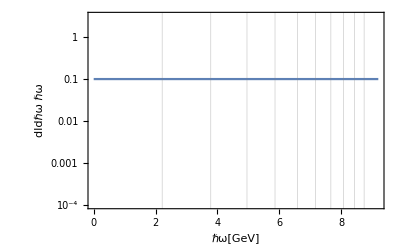

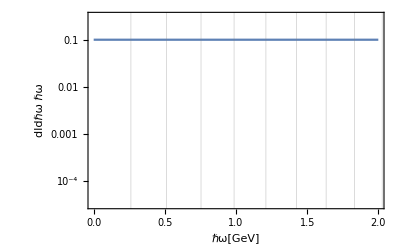

```mathematica
Clear[ℏω,ϵ,m,a0,s,ℏωGeV]
Clear[c,ℏ,m,ℏωsGeV,λμm,ωL,e]

c=3 10^8;(*[m/s]*)
ℏ=1.05 10^-34;(*[Js]*)
m=9.1 10^-31;(*[Kg]*)
e=1.6 10^-19;(*[C]*)

ωL=(2π c)/(λμm 10^-6);(*[1/s]*)

mGeV=0.511 10^-3;(*[GeV]*)
ϵGeV=13;(*[GeV]*)
ℏωGeV=(ℏ ωL)/e 10^-9;(*[GeV?]*)

(* showing harmonics as GridLines *)
a0=1;
ℏωsGeV=Table[((4s ℏωGeV ϵGeV^2)/(mGeV^2(1+a0^2/2)+4 s ℏωGeV ϵGeV)//.{λμm->0.8})//N,{s,1,10}];
LogPlot[{0.1},{ℏω,0,9.2},GridLines->{ℏωsGeV,None},PlotRange->{{0,9.2},{10^-4,10^0.5}},Frame->True,FrameLabel->{"ℏω[GeV]","dIdℏω ℏω"}]

ℏωsGeV=Table[((4s ℏωGeV ϵGeV^2)/(mGeV^2(1+a0^2/2)+4 s ℏωGeV ϵGeV)//.{λμm->8})//N,{s,1,10}];
LogPlot[{0.1},{ℏω,0,2},GridLines->{ℏωsGeV,None},PlotRange->{{0,2},{10^-4.5,10^-0.5}},Frame->True,FrameLabel->{"ℏω[GeV]","dIdℏω ℏω"}]
```

## Figure 2 + Figure 5 (continuation) Formation length

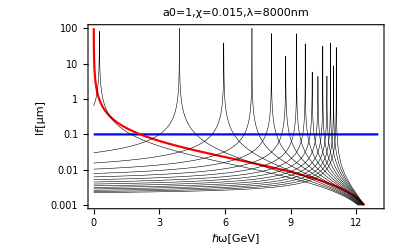

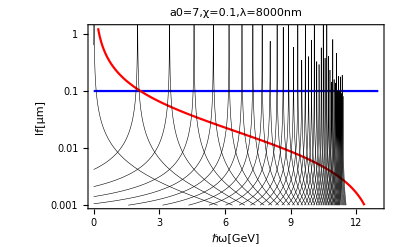

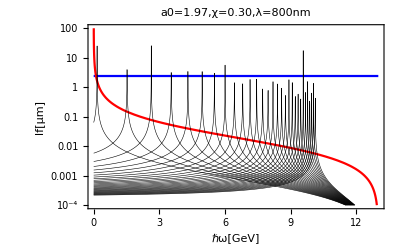

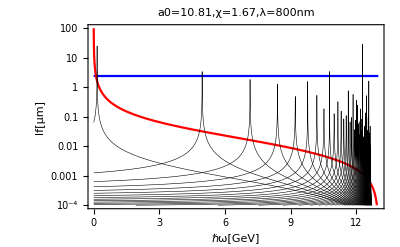

```mathematica
(* "The values of s are not equidistant and are chosen to represent the entire spectrum." *)
Clear[lf,lf39,lf41,a0,ω,ϵ,γ,s,c,ℏ,e,m,ωl,lf39fun,lf41fun,ℏωGeV,λ]
c=3 10^8; (*[m/s]*)
ℏ=1.05 10^-34;(*[Js]*)
e=1.6 10^-19;(*[C]*)
m=9.1 10^-31;(*[Kg]*)

(* eq 39 *)
lf39=2 γ^2(ϵ-ℏ ω)/(ϵ ω);

(* equation 41: LMA effective formation length. use Abs *)
lf41=(2γ^2)/Abs[(ϵ ω(1+a0^2/2))/(ϵ-ℏ ω)-4γ^2 s ωl];

ϵ=13 10^9 e; (*[eV]*)
γ=ϵ/(511 10^3 e);(*[] ~25000 -> 13GeV *)
ωl = 2π c/λ//N;(*[s^-1] ωl is frequency of plane wave background*)


(* Figure 2 *)
λ=8000 10^-9;(*[m] *)
lf39fun=0.3 10^9 10^6 lf39/.{ω->10^9 e ℏωGeV/ℏ};
lf41fun=0.3 10^9 10^6 lf41/.{ω->10^9 e ℏωGeV/ℏ};
a0=1;(*[]*)
Show[{LogPlot[{0.1,lf39fun},{ℏωGeV,0,13},Frame->True,FrameLabel->{"ℏω[GeV]","lf[μm]"},PlotStyle->{Blue,Red,Black},PlotRange->{{0,13},{10^-3,10^2}},PlotLabel->"a0=1,χ=0.015,λ=8000nm"],
LogPlot[Table[lf41fun,{s,1,300,20}],{ℏωGeV,0,13},PlotStyle->{{Black,Thickness[0.001]}},PlotRange->{{0,13},{10^-3,10^2}}]}]
a0=7;
Show[{LogPlot[{0.1,lf39fun},{ℏωGeV,0,13},Frame->True,FrameLabel->{"ℏω[GeV]","lf[μm]"},PlotStyle->{Blue,Red},PlotRange->{{0,13},{10^-3,10^0.1}},PlotLabel->"a0=7,χ=0.1,λ=8000nm"],
LogPlot[Table[lf41fun,{s,1,6000,150}],{ℏωGeV,0,13},PlotStyle->{{Black,Thickness[0.001]}},PlotRange->{{0,13},{10^-3,10^2}}]}]


(* Figure 5 *)
Clear[lf39fun,lf41fun,lf39,lf41]
λ=800 10^-9;(*[m] *)
lf39=2 γ^2(ϵ-ℏ ω)/(ϵ ω);
lf41=(2γ^2)/Abs[(ϵ ω(1+a0^2/2))/(ϵ-ℏ ω)-4γ^2 s ωl];
lf39fun=0.3 10^9 10^6 lf39/.{ω->10^9 e ℏωGeV/ℏ};
lf41fun=0.3 10^9 10^6 lf41/.{ω->10^9 e ℏωGeV/ℏ};
a0=1.97;(*[]*)
Show[{LogPlot[{2.4,lf39fun},{ℏωGeV,0,13},Frame->True,FrameLabel->{"ℏω[GeV]","lf[μm]"},PlotStyle->{Blue,Red,Black},PlotRange->{{0,13},{10^-4,10^2}},PlotLabel->"a0=1.97,χ=0.30,λ=800nm"],
LogPlot[Table[lf41fun,{s,1,300,10}],{ℏωGeV,0,13},PlotStyle->{{Black,Thickness[0.001]}},PlotRange->{{0,13},{10^-4,10^2}}]}]
a0=10.81;
Show[{LogPlot[{2.4,lf39fun},{ℏωGeV,0,13},Frame->True,FrameLabel->{"ℏω[GeV]","lf[μm]"},PlotStyle->{Blue,Red},PlotRange->{{0,13},{10^-4,10^2}},PlotLabel->"a0=10.81,χ=1.67,λ=800nm"],
LogPlot[Table[lf41fun,{s,1,3000,50}],{ℏωGeV,0,13},PlotStyle->{{Black,Thickness[0.001]}},PlotRange->{{0,13},{10^-4,10^2}}]}]
```